```mathematica
kB=1.38065*10^-23;
```

```mathematica
Nav=6.022*10^23;
```

```mathematica
R0=kB*Nav/1000;
```

```mathematica
Needs["PlotLegends`"]
```

### Boltzmann distribution

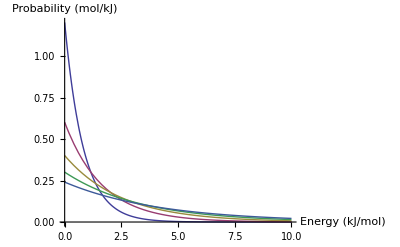

-Graphics-

```mathematica
Plot[Evaluate[Table[Exp[-e /(R0*T)]/(R0  T),{T,100,500,100}]],{e,0,10},PlotRange->All,AxesLabel->{"Energy (kJ/mol)","Probability (mol/kJ)"},PlotLegend->{"100 K","200 K", "300 K","400 K","500 K"}]
```

```mathematica
mass =28*10^-3/Nav;
```

### One-dimensional velocity distribution

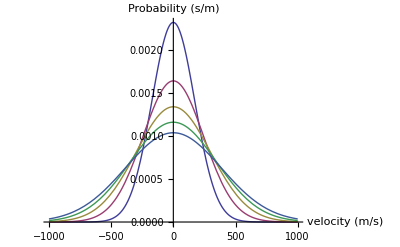

-Graphics-

```mathematica
Plot[Evaluate[Table[Sqrt[mass/(2 Pi kB T)]Exp[-mass vx^2 /(2 kB*T)],{T,100,500,100}]],{vx,-1000,1000},PlotRange->All,AxesLabel->{"velocity (m/s)","Probability (s/m)"},PlotLegend->{"100 K","200 K", "300 K","400 K","500 K"}]
```

### Maxwell-Boltzmann distribution

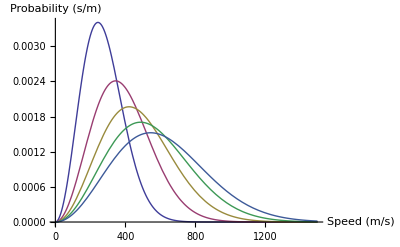

-Graphics-

```mathematica
Plot[Evaluate[Table[4 Pi v^2 (mass/(2 Pi kB T))^1.5 Exp[-mass v^2 /(2 kB*T)],{T,100,500,100}]],{v,0,1500},PlotRange->All,AxesLabel->{"Speed (m/s)","Probability (s/m)"},PlotLegend->{"100 K","200 K", "300 K","400 K","500 K"}]
```

### Diffusion

```mathematica
Dx=1.1*10^-5
```

0.000011

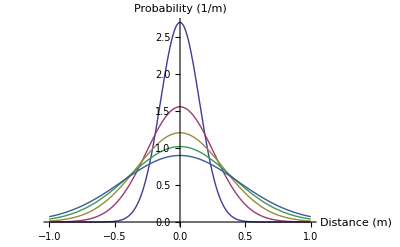

-Graphics-

```mathematica
Plot[Evaluate[Table[1/(2 Sqrt[Pi Dx t])Exp[-x^2 /(4 Dx t)],{t,1000,10000,2000}]],{x,-1,1},PlotRange->All,AxesLabel->{"Distance (m)","Probability (1/m)"},PlotLegend->{"1000 s","2000 s", "3000 s","4000 s","5000 s"}]
```

### Black body

```mathematica
h=6.626*10^-34
```

6.626×10^-34

```mathematica
kBeV=8.61734*10^-5
```

0.0000861734

```mathematica
c=2.994*10^8
```

2.994×10^8

```mathematica
hc=1240
```

1240

```mathematica
Plot[Evaluate[Table[hnu/(Exp[hnu/(kBeV T)]-1)/(kBeV T),{T,100,500,100}]],{hnu,0,0.3},PlotRange->All,AxesLabel->{"h nu (eV)","Energy (kB T)"},PlotLegend->{"100 K","200 K", "300 K","400 K","500 K"}]
```

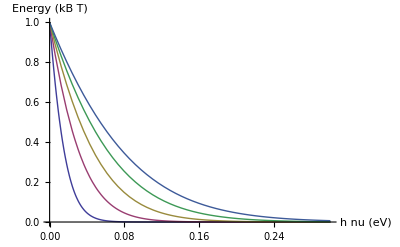

#### Average energy vs. wavelength

```mathematica
Plot[Evaluate[Table[hc/(lambda (Exp[hc/(lambda kBeV T)]-1))/(kBeV T),{T,200,1000,200}]],{lambda,0,300000},PlotRange->All,AxesLabel->{"Wavelength (nm)","Average Energy (kB T)"},PlotLegend->{"200 K","400 K", "600 K","800 K","1000 K"}]
```

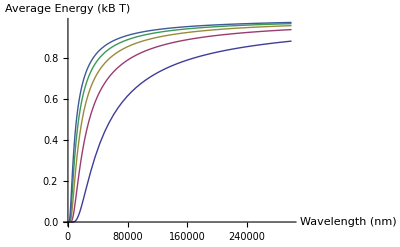

#### Intensity

```mathematica
Plot[Evaluate[Table[(8 Pi/lambda^5)(hc^2/ (Exp[hc/(lambda kBeV T)]-1)),{T,200,1000,200}]],{lambda,0,20000},PlotRange->All,AxesLabel->{"Wavelength (nm)","Intensity"},PlotLegend->{"200 K","400 K", "600 K","800 K","1000 K"}]
```

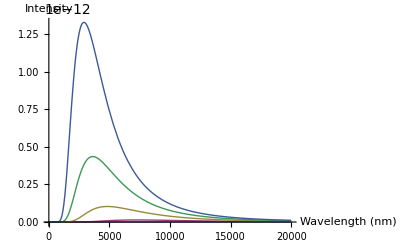

### Einstein model of heat capacity

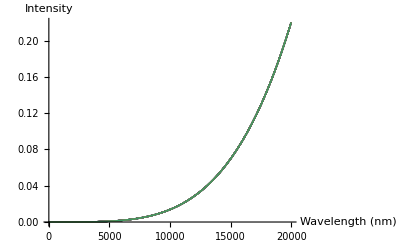

```mathematica
Plot[Evaluate[Table[3 R0(hc/lambda kBeV T)^2(Exp[hc/(lambda kBeV T)] / (Exp[hc/(lambda kBeV T)]-1)^2),{lambda,30000,400000,10000}]],{T,0,20000},PlotRange->All,AxesLabel->{"Wavelength (nm)","Intensity"},PlotLegend->{"200 K","400 K", "600 K","800 K","1000 K"}]
```

```mathematica
1/300
```

1/300

```mathematica
N[%]
```

0.00333333

```mathematica
%/10^-7
```

33333.3